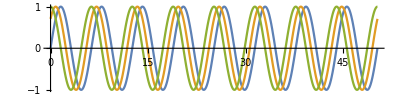

```mathematica
Plot[{Sin[t],Sin[t+Pi/4],Sin[t+Pi/2]},{t,0, 16Pi},AspectRatio->1/4,Ticks->None]
```

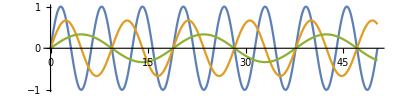

```mathematica
Plot[{Sin[t],2/3 Sin[2t/3],1/3 Sin[t/3]},{t,0, 16Pi},AspectRatio->1/4,Ticks->None]
```

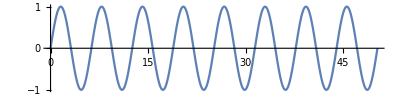

```mathematica
Plot[{Sin[t],None,None},{t,0, 16Pi},AspectRatio->1/4,Ticks->None]
```

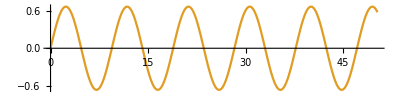

```mathematica
Plot[{None,2/3 Sin[2t/3],None},{t,0, 16Pi},AspectRatio->1/4,Ticks->None]
```

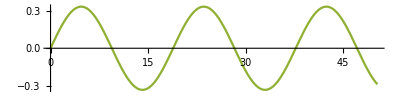

```mathematica
Plot[{None,None,1/3 Sin[t/3]},{t,0, 16Pi},AspectRatio->1/4,Ticks->None]
```

```mathematica
velo[Ω_,R_]:=Ω R
```

```mathematica
circumf[Ω_,R_]:=2Pi R Sqrt[1-velo[Ω,R]^2]
```

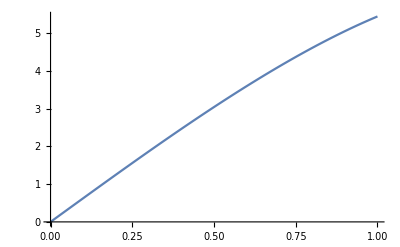

```mathematica
Plot[circumf[0.5,r],{r, 0, 1}]
```

```mathematica
worldline[Ω_,R_,t_,ϕ_]:= R Sin[2Pi(Ω t+ϕ)/circumf[Ω,R]]
```

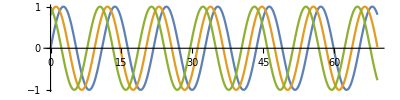

```mathematica
Plot[{worldline[0.5,1,t,0],worldline[0.5,1,t,Pi/4],worldline[0.5,1,t,Pi/2]},{t,0,22Pi},AspectRatio->1/4,Ticks->None]
```

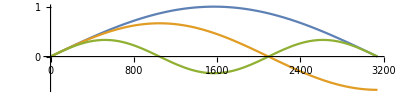

```mathematica
Plot[{worldline[0.001,1,t,0],worldline[0.001,2/3,t,0],worldline[0.001,1/3,t,0]},{t,0,1000Pi},AspectRatio->1/4,Ticks->None]
```

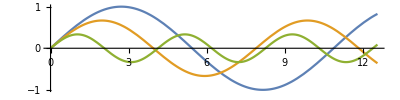

```mathematica
Plot[{worldline[0.5,1,t,0],worldline[0.5,2/3,t,0],worldline[0.5,1/3,t,0]},{t,0,4Pi},AspectRatio->1/4,Ticks->None]
```

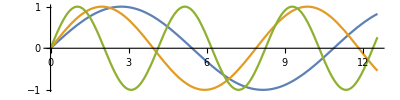

```mathematica
Plot[{worldline[0.5,1,t,0],3/2 worldline[0.5,2/3,t,0],3worldline[0.5,1/3,t,0]},{t,0,4Pi},AspectRatio->1/4,Ticks->None]
```

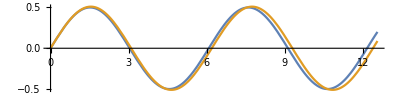

```mathematica
Plot[{worldline[0.5,0.5,t,0],worldline[0.5,0.51,t,0]},{t,0,4Pi},AspectRatio->1/4,Ticks->None]
```